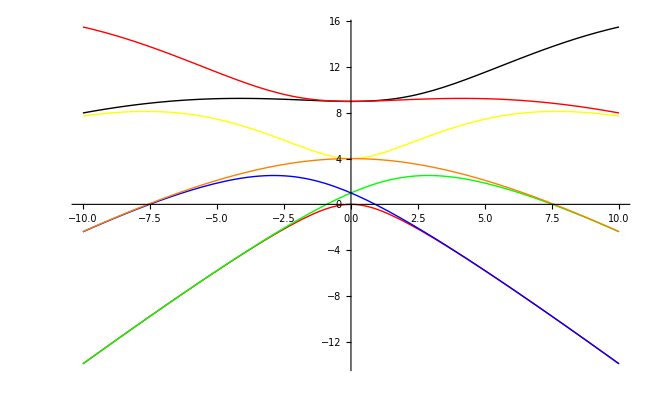

```mathematica
Plot[{MathieuCharacteristicA[0,q],MathieuCharacteristicA[1,q],MathieuCharacteristicB[1,q],MathieuCharacteristicA[2,q],MathieuCharacteristicB[2,q],MathieuCharacteristicA[3,q],MathieuCharacteristicB[3,q]},{q,-10,10},PlotStyle->{Red,Green,Blue,Yellow,Orange,Black}]
```

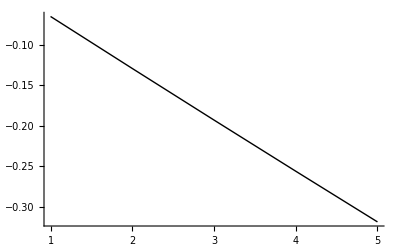

```mathematica
fx[n_,q_]:=(MathieuCharacteristicA[n,q]-MathieuCharacteristicA[0,q])/MathieuCharacteristicA[0,q];
ListPlot[Table[fx[n,1000],{n,1,5}],PlotStyle->{Red,Green,Blue,Yellow,Orange,Black},PlotRange->All,Joined->True]
```

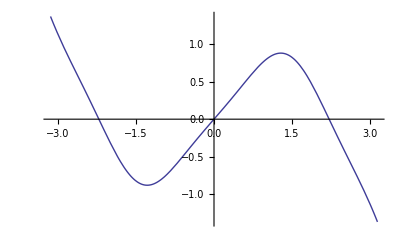

```mathematica
Plot[{Im[MathieuS[1,1,x]]},{x,-π,π}]
```

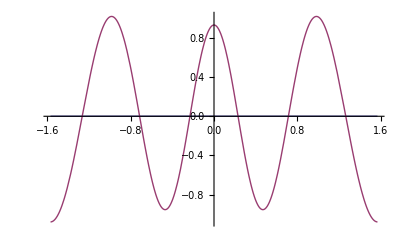

```mathematica
Plot[{0,Re[MathieuC[MathieuCharacteristicA[6,-5],-5,x]]},{x,-π/2,π/2},PlotRange->All]
```

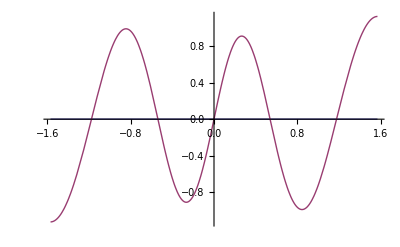

```mathematica
Plot[{0,MathieuS[MathieuCharacteristicB[5,-5],-5,x]},{x,-π/2,π/2},PlotRange->All]
```

```mathematica
N[MathieuS[MathieuCharacteristicB[2,-5],-5,π]]
```

-5.10118×10^-16+6.61744×10^-24 ⅈ

```mathematica
data=Import["POLLT6.dat"];
```

```mathematica
Clear[len];
len=Length[data]
```

500

```mathematica
Clear[avgcorr11,avgcorr12,avgcorr21,avgcorr22];
Clear[errcorr11,errcorr12,errcorr21,errcorr22];
Clear[eval,eval1,eval2];
TMAX=5;
For[t=1,t≤TMAX,t++,
Clear[corr11,corr12,corr21,corr22];
corr11=Table[data[[n,2]],{n,t,500,5}];
corr12=Table[data[[n,3]],{n,t,500,5}];
corr21=Table[data[[n,4]],{n,t,500,5}];
corr22=Table[data[[n,5]],{n,t,500,5}];
avgcorr11[t]=Mean[corr11];
errcorr11[t]=Sqrt[StandardDeviation[corr11]/len];
avgcorr12[t]=Mean[corr12];
errcorr12[t]=Sqrt[StandardDeviation[corr12]/len];
avgcorr21[t]=Mean[corr21];
errcorr21[t]=Sqrt[StandardDeviation[corr21]/len];
avgcorr22[t]=Mean[corr22];
errcorr22[t]=Sqrt[StandardDeviation[corr22]/len];
]
(* Print the correlation matrix *)
For[t=1,t≤TMAX,t++,
(*Print[t," ",avgcorr11[t]," ",avgcorr12[t]," ",avgcorr21[t]," ",avgcorr22[t]];*)
Clear[mat];
mat={{avgcorr11[t],avgcorr12[t]},{avgcorr21[t],avgcorr22[t]}};
(*Print[MatrixForm[mat]];*)
eval=Eigenvalues[mat];
eval1[t]=eval[[1]];
eval2[t]=eval[[2]];
]
```

{0.0000250015,6.25032×10^-10,1.56256×10^-14,3.90629×10^-19,9.76538×10^-24}

{2.34323×10^-9,6.24847×10^-14,1.56204×10^-18,3.90511×10^-23,9.76242×10^-28}

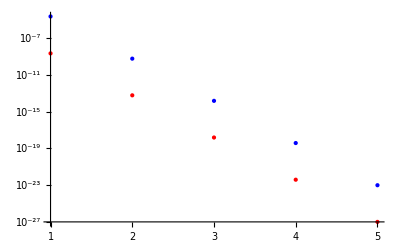

```mathematica
e1=Table[eval1[t],{t,1,5}]
e2=Table[-eval2[t],{t,1,5}]
ListLogPlot[{e1,e2},PlotStyle->{{PointSize[Large],Blue},{PointSize[Large],Red}}]
```